```mathematica
Quit
```

The notebook presents the computation of the spin corrections to the partial amplitudes and fluxes in the Hamilton-Jacobi formalism. See arXiv:2410.05769 (https://arxiv.org/abs/2410.05769v1 )
Specifically, it includes:
- examples on how to use the package SpinOrbitsHamiltonJacobi,
- examples on how to use the package TeukolskySpinFluxesHamiltonJacobi
- comparisons with the results of Skoupý et at, PRD 108, 044041 (https://journals.aps.org/prd/abstract/10.1103/PhysRevD.108.044041 )
- computation of the corrections due spin precession on the asymptotic partial amplitudes
- computation of waveform snapshots
- some convergence tests of the amplitudes and fluxes in terms of the Fourier harmonics modes in the orbits  (see the “Convergence tests” chapter)

PREREQUISITEs: the following packages are needed
-  SpinOrbitsHamiltonJacobi
- KerrGeodesics from the BPToolkit. This package is only needed for testing

```mathematica
(*PacletDataRebuild[]*)
```

If you make use of this notebook, please acknowledge 
- "Piovano, Pantelidou, Mac Uilliam and Witzany“ arXiv:2410.05769 (https://arxiv.org/abs/2410.05769v1 )
- “Piovano” arXiv: ()
- KerrGeodesics package,  (https://zenodo.org/records/8108265) of the  BHPToolkit

IMPORTANT NOTE: all the functions for the orbits take as input the mean anomalies w_r. The input of the following functions are:

- primary spin “a”
- semi-latus rectum “p”
- eccentricity “e”
- inclination “x” defined as  x=Sign[L_z]√(1-z_1^2)

### Convention for EoM

Here we follow the same convention of  CQG, Volume 37, Number 14  (https://iopscience.iop.org/article/10.1088/1361-6382/ab79d5 )

r_1== p/(1-e)
r_2== p/(1+e)
z_1==√(1-x^2)

or

p==2(r_1 r_2)/(r_1+r_2)
e== (r_1-r_2)/(r_1+r_2)
x ==  Sign[ℒ]√(1-z_1^2)

(circular) 0<e<1 (parabolic)
(retrograde) -1 < x < 1 (prograde)
p> p_LSO(e,x)

Equatorial orbits

x==±1
z_1==0
𝒬 ==0

“spar” and “sort” are the parallel and orthogonal component of the spin to the total angular momentum.

### Loading all the necessary files

```mathematica
SetDirectory[NotebookDirectory[]];
```

```mathematica
<<KerrGeodesics`
```

```mathematica
Get["AnalyticSpinOrbitsHamiltonJacobi.wl"]
```

```mathematica
Get["SpinOrbitsHamiltonJacobi.wl"]
```

## Periodic orbits, fixed turning points

### Calculation orbits

```mathematica
AbsoluteTiming[corrDHGeneric=KerrSpinOrbitCorrectionDHPar[0.9`45,12`45,0.2`45,0.99995`45,12,12];]
```

Calculating ξ_r, ξ_z Fourier coefficients

Calculating Fourier coefficients of dt_s/dλ

Calculating Fourier coefficients of dϕ_s/dλ

{12.6485,Null}

```mathematica
AbsoluteTiming[corrDH=KerrNearEqSpinOrbitCorrDHPer[0.9`45,12`45,0.2`45,1];]
```

{0.006155,Null}

```mathematica
AbsoluteTiming[corrDHFourier=KerrNearEqSpinOrbitCorrDHPerFourier[0.9`45,12`45,0.2`45,1,12];]
```

Calculating Fourier coefficients of dt_s/dλ

Calculating Fourier coefficients of dϕ_s/dλ

{0.068944,Null}

### Constants of motion and frequencies

```mathematica
{corrDHGeneric["Eg"],corrDHGeneric["Lzg"]}
```

{0.9614729536603698436559687929905600088214798,3.74723231257944865174688188760482748674875}

```mathematica
{corrDH["Eg"],corrDH["Lzg"]}
```

{0.96147287235996815807541717873449397423418686,3.74740955904619046614861813959055232913293}

```mathematica
{corrDHFourier["Eg"],corrDHFourier["Lzg"]}
```

{0.96147287235996815807541717873449397423418686,3.74740955904619046614861813959055232913293}

Mino-time frequencies. Order of appearance: Υ_t , Υ_r , Υ_z , Υ_ϕ

```mathematica
corrDHGeneric["MinoFrequenciesGeo"]
```

{174.217921188164503961316791317149680179,3.154065958855754796930156708864380652914,3.755577549373545158491631615020650525204,3.8944365532636629446606795563707983404}

```mathematica
corrDH["MinoFrequenciesGeo"]
```

{174.2178489847441271099172448080513484331,3.1540761630775864787744331028084859702835,3.75556787116950135091509572396550808810016,3.89442518256694996059374532370892282}

```mathematica
corrDHFourier["MinoFrequenciesGeo"]
```

{174.2178489847441271099172448080513484331,3.1540761630775864787744331028084859702835,3.75556787116950135091509572396550808810016,3.89442518256694996059374532370892282}

BL frequencies. Order of appearance:  Ω_r , Ω_z , Ω_ϕ

```mathematica
corrDHGeneric["BLFrequenciesGeo"]
```

{0.0181041418548967641805241919000283330615,0.0215567808624999272060910775355020792165,0.022353822882879350570740389330114969809}

```mathematica
corrDH["BLFrequenciesGeo"]
```

{0.01810420792965812575108148504132270651606,0.02155673424425282709391453340015457035778,0.0223537668801546056669080200937407272107}

```mathematica
corrDHFourier["BLFrequenciesGeo"]
```

{0.01810420792965812575108148504132270651606,0.02155673424425282709391453340015457035778,0.0223537668801546056669080200937407272107}

### Oscillating terms geodesic coordinate time and azimuthal trajectories

```mathematica
{corrDHGeneric[ "Δtrg"][23π/5],corrDHGeneric[ "Δϕrg"][23π/5]}
```

{-19.958320126815007083213106650272756255,0.008991601077418069540782913317929388546}

```mathematica
{corrDH[ "Δtrg"][23π/5],corrDH[ "Δϕrg"][23π/5]}
```

{-19.9582565521006256323120012231432076,0.00899141590656161755013026598845084}

```mathematica
{corrDHFourier[ "Δtrg"][23π/5],corrDHFourier[ "Δϕrg"][23π/5]}
```

{-19.9582565521167721361197665087030082169,0.0089914159065616183422214683000566223619}

### Shifts constants of motion

```mathematica
{corrDHGeneric["Es"],corrDHGeneric["Jzs"]}
```

{-0.00090333544045869956894990573711315746654,0.8488981743617680312958926298711500790508}

```mathematica
{corrDH["Es"],corrDH["Jzs"]}
```

{-0.00090332773940690798757401021507643834531959,0.848979338634238967083302020562659910836728}

```mathematica
{corrDHFourier["Es"],corrDHFourier["Jzs"]}
```

{-0.00090332773940690798757401021507643834531959,0.848979338634238967083302020562659910836728}

### Shifts frequencies

Mino-time frequencies. Order of appearance: Υ_t , Υ_r , Υ_z , Υ_ϕ

```mathematica
corrDHGeneric["MinoFrequenciesCorrection"]
```

{-0.245437788860093653677689704486,0.12346078985803258802432937915028,-0.04594215674339090271105537431405,-0.1138965459671304489075482137656308}

```mathematica
corrDH["MinoFrequenciesCorrection"]
```

{-0.24543745342018557306469916422355340081,0.123459407486065720506054255924305839226,-0.11389245330810692289765426354282229481}

```mathematica
corrDHFourier["MinoFrequenciesCorrection"]
```

{-0.2454374534201855730646991642235534008,0.123459407486065720506054255924305839226,-0.113892453308106922897654263542822294805}

BL frequencies. Order of appearance: Ω_r , Ω_z , Ω_ϕ

```mathematica
corrDHGeneric["BLFrequenciesCorrection"]
```

{0.00073416230392259495831740313765574,-0.0002333359727651197860534359702654,-0.00062226705706755509217105509877981}

```mathematica
corrDH["BLFrequenciesCorrection"]
```

{0.000734154731687168932405034673488462226673,-0.00062224394528132513233871945455750276689}

```mathematica
corrDHFourier["BLFrequenciesCorrection"]
```

{0.000734154731687168932405034673488462226673,-0.00062224394528132513233871945455750276689}

### Spin corrections parallel component of the spin

#### Spin corrections to the radial trajectories

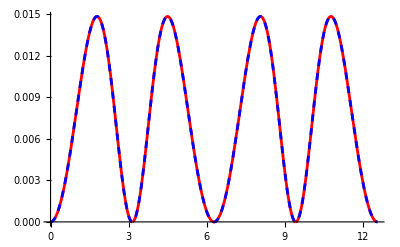

```mathematica
Show[Plot[corrDH["δrpar"][wr],{wr,0,4π},PlotStyle->Red],Plot[corrDHGeneric["δrpar"][wr,23],{wr,0,4π},PlotStyle->{Blue,Dashed}]]
```

```mathematica
Show[Plot[corrDHFourier["δrpar"][wr],{wr,0,4π},PlotStyle->Red],Plot[corrDHGeneric["δrpar"][wr,23],{wr,0,4π},PlotStyle->{Blue,Dashed}]]
```

-Graphics-

#### Spin corrections to the radial velocities

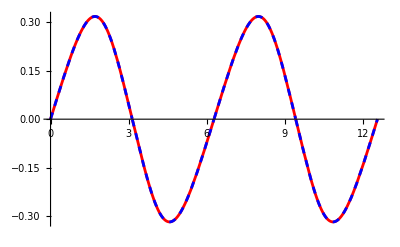

```mathematica
Show[Plot[corrDH["δvrpar"][wr],{wr,0,4π},PlotStyle->Red],Plot[corrDHGeneric["δvrpar"][wr,23],{wr,0,4π},PlotStyle->{Blue,Dashed}]]
```

```mathematica
Show[Plot[corrDHFourier["δvrpar"][wr],{wr,0,4π},PlotStyle->Red],Plot[corrDHGeneric["δvrpar"][wr,23],{wr,0,4π},PlotStyle->{Blue,Dashed}]]
```

-Graphics-

#### Spin corrections to the coordinate time and azimuthal trajectories - purely oscillatory term

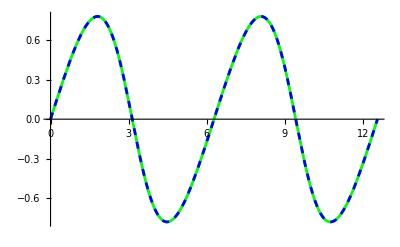

```mathematica
Show[Plot[corrDH["Δδtpar"][wr],{wr,0,4π},PlotStyle->Green],Plot[corrDHGeneric["Δδtpar"][wr,23],{wr,0,4π},PlotStyle->{Blue,Dashed}]]
```

```mathematica
corrDHGeneric["Δδtpar"][wr,0]//Simplify//N
```

0.768063 Sin[wr]-0.180474 Cos[wr] Sin[wr]+0.0117228 Sin[3. wr]-0.00151909 Sin[4. wr]+0.000192944 Sin[5. wr]-0.0000240353 Sin[6. wr]+2.94535×10^-6 Sin[7. wr]-3.56073×10^-7 Sin[8. wr]+4.25682×10^-8 Sin[9. wr]-5.04178×10^-9 Sin[10. wr]+5.9248×10^-10 Sin[11. wr]-6.91609×10^-11 Sin[12. wr]

```mathematica
corrDHFourier["Δδtpar"][wr]//Simplify//N
```

0.768051 Sin[wr]-0.18047 Cos[wr] Sin[wr]+0.0117225 Sin[3. wr]-0.00151905 Sin[4. wr]+0.000192939 Sin[5. wr]-0.0000240346 Sin[6. wr]+2.94525×10^-6 Sin[7. wr]-3.56061×10^-7 Sin[8. wr]+4.25667×10^-8 Sin[9. wr]-5.04159×10^-9 Sin[10. wr]+5.92456×10^-10 Sin[11. wr]-6.9158×10^-11 Sin[12. wr]

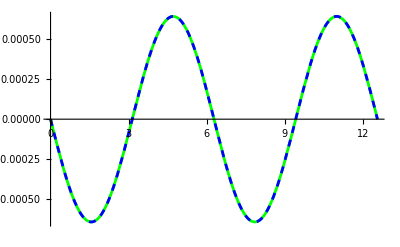

```mathematica
Show[Plot[corrDH["Δδϕpar"][wr],{wr,0,4π},PlotStyle->Green],Plot[corrDHGeneric["Δδϕpar"][wr,23],{wr,0,4π},PlotStyle->{Blue,Dashed}]]
```

```mathematica
corrDHGeneric["Δδϕpar"][wr,0]//Simplify//N
```

-0.000643821 Sin[wr]-2.24023×10^-6 Cos[wr] Sin[wr]-5.38528×10^-7 Sin[3. wr]-2.15984×10^-10 Sin[4. wr]+2.60725×10^-13 Sin[5. wr]-1.05419×10^-14 Sin[6. wr]-3.93501×10^-17 Sin[7. wr]

```mathematica
corrDHFourier["Δδϕpar"][wr]//Simplify//N
```

-0.000643766 Sin[wr]-2.22529×10^-6 Cos[wr] Sin[wr]-5.38344×10^-7 Sin[3. wr]-2.16501×10^-10 Sin[4. wr]+2.50866×10^-13 Sin[5. wr]-1.04769×10^-14 Sin[6. wr]-3.97182×10^-17 Sin[7. wr]

#### Spin corrections to the coordinate time and azimuthal velocities

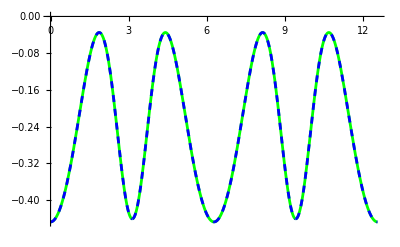

```mathematica
Show[Plot[corrDH["δvtpar"][wr],{wr,0,4π},PlotStyle->Green],Plot[corrDHGeneric["δvtpar"][wr,23],{wr,0,4π},PlotStyle->{Blue,Dashed}]]
```

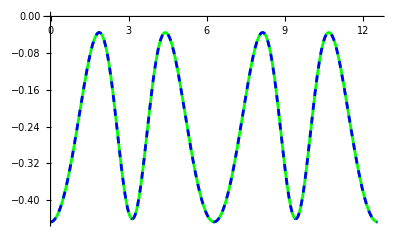

```mathematica
Show[Plot[corrDHFourier["δvtpar"][wr],{wr,0,4π},PlotStyle->Green],Plot[corrDHGeneric["δvtpar"][wr,23],{wr,0,4π},PlotStyle->{Blue,Dashed}]]
```

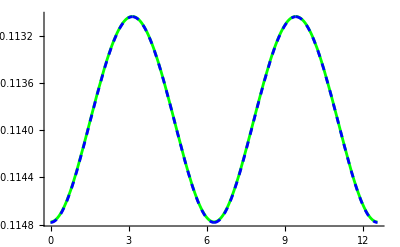

```mathematica
Show[Plot[corrDH["δvϕpar"][wr],{wr,0,4π},PlotStyle->Green],Plot[corrDHGeneric["δvϕpar"][wr,23],{wr,0,4π},PlotStyle->{Blue,Dashed}]]
```

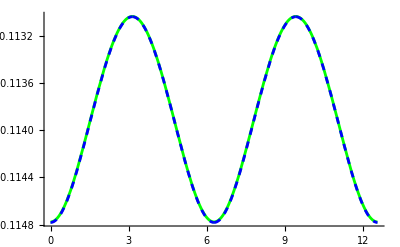

```mathematica
Show[Plot[corrDHFourier["δvϕpar"][wr],{wr,0,4π},PlotStyle->Green],Plot[corrDHGeneric["δvϕpar"][wr,23],{wr,0,4π},PlotStyle->{Blue,Dashed}]]
```

### Spin corrections orthogonal component of the spin

Mino-time precession frequency

```mathematica
corrFC["MinoPrecessionFrequency"]
```

corrFC[MinoPrecessionFrequency]

Precession phase

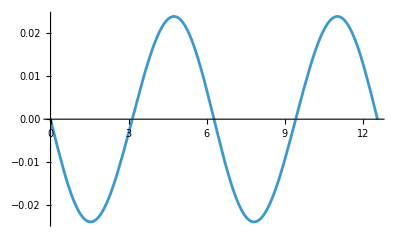

```mathematica
Plot[corrDH["ψp"][wr],{wr,0,4π}]
```

Spin correction to the polar motion

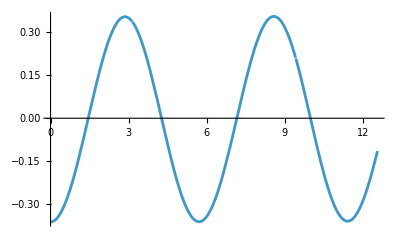

```mathematica
Plot[corrDH["δzort"][wr],{wr,0,4π}]
```

## Periodic orbits, fixed constants of motion

### Calculation orbits

```mathematica
AbsoluteTiming[corrFCGeneric=KerrSpinOrbitCorrectionFCPar[0.9`45,12`45,0.2`45,0.9999995`45,12,12];]
```

Calculating ξ_r, ξ_z Fourier coefficients

Calculating Fourier coefficients of dt_s/dλ

Calculating Fourier coefficients of dϕ_s/dλ

{12.8448,Null}

```mathematica
AbsoluteTiming[corrFC=KerrNearEqSpinOrbitCorrFCPer[0.9`45,12`45,0.2`45,1];]
```

{0.00616,Null}

```mathematica
AbsoluteTiming[corrFCFourier=KerrNearEqSpinOrbitCorrFCPerFourier[0.9`45,12`45,0.2`45,1,12];]
```

Calculating Fourier coefficients of dt_s/dλ

Calculating Fourier coefficients of dϕ_s/dλ

{0.071831,Null}

### Constants of motion and frequencies

```mathematica
{corrFCGeneric["Eg"],corrFCGeneric["Lzg"]}
```

{0.9614728731729632140549897788948365003453999,3.74740778658555061418910966739383604101196}

```mathematica
{corrFC["Eg"],corrFC["Lzg"]}
```

{0.96147287235996815807541717873449397423418686,3.74740955904619046614861813959055232913293}

```mathematica
{corrFCFourier["Eg"],corrFCFourier["Lzg"]}
```

{0.96147287235996815807541717873449397423418686,3.74740955904619046614861813959055232913293}

Mino-time frequencies. Order of appearance: Υ_t , Υ_r , Υ_z , Υ_ϕ

```mathematica
corrFCGeneric["MinoFrequenciesGeo"]
```

{174.2178497067895327852968125615442805,3.154076061037059245900284936787920376491,3.7555679679504412060456377848971524272,3.8944252962727999709100904312496926198}

```mathematica
corrFC["MinoFrequenciesGeo"]
```

{174.2178489847441271099172448080513484331,3.1540761630775864787744331028084859702835,3.75556787116950135091509572396550808810016,3.89442518256694996059374532370892282}

```mathematica
corrFCFourier["MinoFrequenciesGeo"]
```

{174.2178489847441271099172448080513484331,3.1540761630775864787744331028084859702835,3.75556787116950135091509572396550808810016,3.89442518256694996059374532370892282}

BL frequencies. Order of appearance: Ω_r , Ω_z , Ω_ϕ

```mathematica
corrFCGeneric["BLFrequenciesGeo"]
```

{0.018104207268918783682451523148028937956,0.021556734710427786028317869547410621832,0.02235376744017423338683376637143432684}

```mathematica
corrFC["BLFrequenciesGeo"]
```

{0.01810420792965812575108148504132270651606,0.02155673424425282709391453340015457035778,0.0223537668801546056669080200937407272107}

```mathematica
corrFCFourier["BLFrequenciesGeo"]
```

{0.01810420792965812575108148504132270651606,0.02155673424425282709391453340015457035778,0.0223537668801546056669080200937407272107}

### Oscillating terms geodesic coordinate time and azimuthal trajectories

```mathematica
{corrFC[ "Δtrg"][23π/5],corrFC[ "Δϕrg"][23π/5]}
```

{-19.9582565521006256323120012231432076,0.00899141590656161755013026598845084}

```mathematica
{corrFCFourier[ "Δtrg"][23π/5],corrFCFourier[ "Δϕrg"][23π/5]}
```

{-19.9582565521167721361197665087030082169,0.0089914159065616183422214683000566223619}

```mathematica
{corrFCGeneric[ "Δtrg"][23π/5],corrFCGeneric[ "Δϕrg"][23π/5]}
```

{-19.958257187850997096414755408098740591,0.008991417758255493819769074890418345751}

### Shifts frequencies

Mino-time frequencies. Order of appearance: Υ_t , Υ_r , Υ_z , Υ_ϕ

```mathematica
corrFCGeneric["MinoFrequenciesCorrection"]
```

{-47.6353457336316001559974622648638,-0.8705340792813652152944579285105056,-0.89326033857603472791534204241,-0.8703905471252491575359567820543059}

```mathematica
corrFC["MinoFrequenciesCorrection"]
```

{-47.6353315716074272230027686768761225185,-0.870533843581772020603215744864336441255,-0.87039039145955093191431276342496545192}

```mathematica
corrFCFourier["MinoFrequenciesCorrection"]
```

{-47.635331571607427223002768676876122519,-0.870533843581772020603215744864336441255,-0.8703903914595509319143127634249654519231}

BL frequencies. Order of appearance:  Ω_r , Ω_z , Ω_ϕ

```mathematica
corrFCGeneric["BLFrequenciesCorrection"]
```

{-0.00004668813675970676793726259557929,0.0007668684492904922956396767964,0.00111606757667994515032733179150427}

```mathematica
corrFC["BLFrequenciesCorrection"]
```

{-0.0000466880750656899360945712368510409165,0.001116066504575296323638742760698419946}

```mathematica
corrFCFourier["BLFrequenciesCorrection"]
```

{-0.0000466880750656899360945712368510409165,0.001116066504575296323638742760698419946}

### Spin corrections parallel component of the spin

#### Spin corrections to the radial trajectories

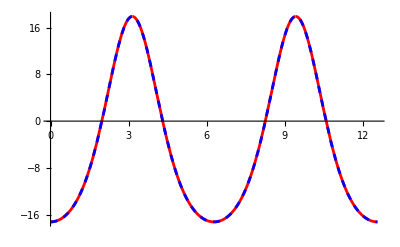

```mathematica
Show[Plot[corrFC["δrpar"][wr],{wr,0,4π},PlotStyle->Red],Plot[corrFCGeneric["δrpar"][wr,23],{wr,0,4π},PlotStyle->{Blue,Dashed}]]
```

```mathematica
Show[Plot[corrFCFourier["δrpar"][wr],{wr,0,4π},PlotStyle->Red],Plot[corrFCGeneric["δrpar"][wr,23],{wr,0,4π},PlotStyle->{Blue,Dashed}]]
```

-Graphics-

#### Spin corrections to the radial velocities

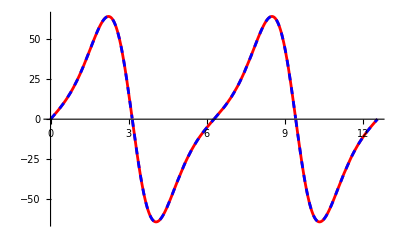

```mathematica
Show[Plot[corrFC["δvrpar"][wr],{wr,0,4π},PlotStyle->Red],Plot[corrFCGeneric["δvrpar"][wr,23],{wr,0,4π},PlotStyle->{Blue,Dashed}]]
```

```mathematica
Show[Plot[corrFCFourier["δvrpar"][wr],{wr,0,4π},PlotStyle->Red],Plot[corrFCGeneric["δvrpar"][wr,23],{wr,0,4π},PlotStyle->{Blue,Dashed}]]
```

-Graphics-

#### Spin corrections to the coordinate time and azimuthal trajectories - purely oscillatory term

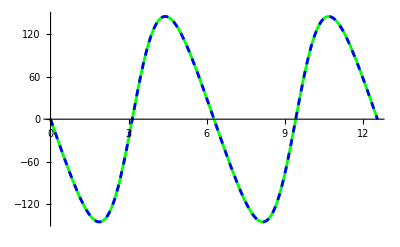

```mathematica
Show[Plot[corrFC["Δδtpar"][wr],{wr,0,4π},PlotStyle->Green],Plot[corrFCGeneric["Δδtpar"][wr,23],{wr,0,4π},PlotStyle->{Blue,Dashed}]]
```

```mathematica
corrFCGeneric["Δδtpar"][wr,0]//Simplify//N
```

-141.26 Sin[wr]+43.7672 Cos[wr] Sin[wr]-3.07619 Sin[3. wr]+0.408892 Sin[4. wr]-0.0524079 Sin[5. wr]+0.0065473 Sin[6. wr]-0.000802557 Sin[7. wr]+0.0000969442 Sin[8. wr]-0.0000115746 Sin[9. wr]+1.36888×10^-6 Sin[10. wr]-1.60623×10^-7 Sin[11. wr]+1.87224×10^-8 Sin[12. wr]

```mathematica
corrFCFourier["Δδtpar"][wr]//Simplify//N
```

-141.26 Sin[wr]+43.7672 Cos[wr] Sin[wr]-3.07619 Sin[3. wr]+0.408892 Sin[4. wr]-0.0524079 Sin[5. wr]+0.0065473 Sin[6. wr]-0.000802556 Sin[7. wr]+0.0000969441 Sin[8. wr]-0.0000115746 Sin[9. wr]+1.36888×10^-6 Sin[10. wr]-1.60623×10^-7 Sin[11. wr]+1.87224×10^-8 Sin[12. wr]

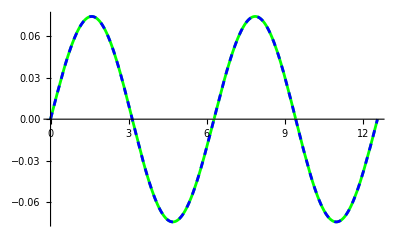

```mathematica
Show[Plot[corrFC["Δδϕpar"][wr],{wr,0,4π},PlotStyle->Green],Plot[corrFCGeneric["Δδϕpar"][wr,23],{wr,0,4π},PlotStyle->{Blue,Dashed}]]
```

```mathematica
corrFCGeneric["Δδϕpar"][wr,0]//Simplify//N
```

0.0745298 Sin[wr]-0.000839241 Cos[wr] Sin[wr]-2.39121×10^-6 Sin[3. wr]-2.22347×10^-10 Sin[4. wr]-1.4204×10^-11 Sin[5. wr]-1.19228×10^-13 Sin[6. wr]-1.14264×10^-16 Sin[7. wr]

```mathematica
corrFCFourier["Δδϕpar"][wr]//Simplify//N
```

0.0745298 Sin[wr]-0.000839241 Cos[wr] Sin[wr]-2.39121×10^-6 Sin[3. wr]-2.2236×10^-10 Sin[4. wr]-1.42041×10^-11 Sin[5. wr]-1.19228×10^-13 Sin[6. wr]-1.14268×10^-16 Sin[7. wr]

#### Spin corrections to the coordinate time and azimuthal velocities

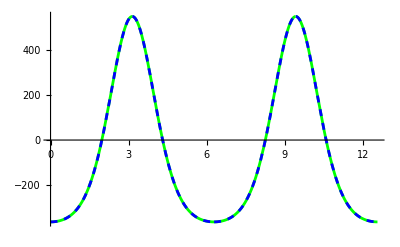

```mathematica
Show[Plot[corrFC["δvtpar"][wr],{wr,0,4π},PlotStyle->Green],Plot[corrFCGeneric["δvtpar"][wr,23],{wr,0,4π},PlotStyle->{Blue,Dashed}]]
```

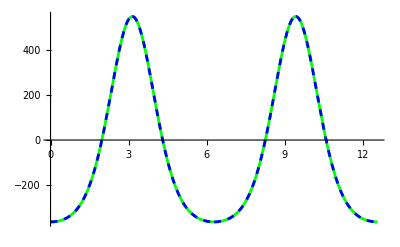

```mathematica
Show[Plot[corrFCFourier["δvtpar"][wr],{wr,0,4π},PlotStyle->Green],Plot[corrFCGeneric["δvtpar"][wr,23],{wr,0,4π},PlotStyle->{Blue,Dashed}]]
```

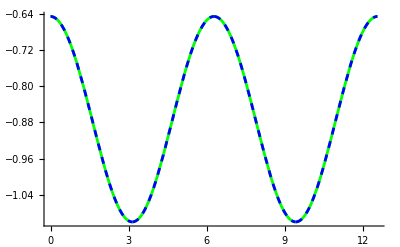

```mathematica
Show[Plot[corrFC["δvϕpar"][wr],{wr,0,4π},PlotStyle->Green],Plot[corrFCGeneric["δvϕpar"][wr,23],{wr,0,4π},PlotStyle->{Blue,Dashed}]]
```

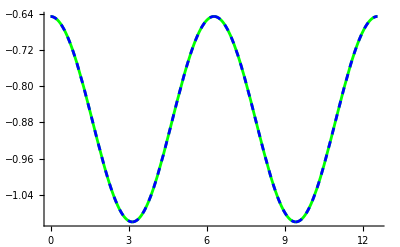

```mathematica
Show[Plot[corrFCFourier["δvϕpar"][wr],{wr,0,4π},PlotStyle->Green],Plot[corrFCGeneric["δvϕpar"][wr,23],{wr,0,4π},PlotStyle->{Blue,Dashed}]]
```

### Spin corrections orthogonal component of the spin

Mino-time precession frequency

```mathematica
corrFC["MinoPrecessionFrequency"]
```

3.467352990830548192488680888772287250288

Precession phase

```mathematica
Plot[corrFC["ψp"][wr],{wr,0,4π}]
```

-Graphics-

Spin correction to the polar motion

```mathematica
Plot[corrFC["δzort"][wr],{wr,0,4π}]
```

-Graphics-

## Periodic orbits, physical and continuous gauge

### Calculation orbits

```mathematica
AbsoluteTiming[corrPCGeneric=KerrSpinOrbitCorrectionPCParEq[0.9`45,12`45,0.2`45,1,12];]
```

Calculating ξ_r Fourier coefficients

Calculating Fourier coefficients of dt_s/dλ

Calculating Fourier coefficients of dϕ_s/dλ

{0.073008,Null}

```mathematica
AbsoluteTiming[corrPC=KerrNearEqSpinOrbitCorrPCPer[0.9`45,12`45,0.2`45,1];]
```

{0.010585,Null}

```mathematica
AbsoluteTiming[corrPCFourier=KerrNearEqSpinOrbitCorrPCPerFourier[0.9`45,12`45,0.2`45,1,12];]
```

Calculating Fourier coefficients of dt_s/dλ

Calculating Fourier coefficients of dϕ_s/dλ

{0.082419,Null}

### Constants of motion and frequencies

```mathematica
{corrPCGeneric["Eg"],corrPCGeneric["Lzg"]}
```

{0.96147287235996815807541717873449397423418686,3.74740955904619046614861813959055232913293}

```mathematica
{corrPC["Eg"],corrPC["Lzg"]}
```

{0.96147287235996815807541717873449397423418686,3.74740955904619046614861813959055232913293}

```mathematica
{corrPCFourier["Eg"],corrPCFourier["Lzg"]}
```

{0.96147287235996815807541717873449397423418686,3.74740955904619046614861813959055232913293}

Mino-time frequencies. Order of appearance: Υ_t , Υ_r , Υ_z , Υ_ϕ

```mathematica
corrPCGeneric["MinoFrequenciesGeo"]
```

{174.217848984744127109917244808051348433,3.154076163077586478774433102808485970283,3.89442518256694996059374532370892282}

```mathematica
corrPC["MinoFrequenciesGeo"]
```

{174.2178489847441271099172448080513484331,3.1540761630775864787744331028084859702835,3.75556787116950135091509572396550808810016,3.89442518256694996059374532370892282}

```mathematica
corrPCFourier["MinoFrequenciesGeo"]
```

{174.2178489847441271099172448080513484331,3.1540761630775864787744331028084859702835,3.75556787116950135091509572396550808810016,3.89442518256694996059374532370892282}

BL frequencies. Order of appearance: Ω_t , Ω_r , Ω_z , Ω_ϕ

```mathematica
corrPCGeneric["BLFrequenciesGeo"]
```

{0.0181042079296581257510814850413227065161,0.022353766880154605666908020093740727211}

```mathematica
corrPC["BLFrequenciesGeo"]
```

{0.01810420792965812575108148504132270651606,0.02155673424425282709391453340015457035778,0.0223537668801546056669080200937407272107}

```mathematica
corrPCFourier["BLFrequenciesGeo"]
```

{0.01810420792965812575108148504132270651606,0.02155673424425282709391453340015457035778,0.0223537668801546056669080200937407272107}

### Oscillating terms geodesic coordinate time and azimuthal trajectories

```mathematica
{corrPCGeneric[ "Δtrg"][23π/5],corrPCGeneric[ "Δϕrg"][23π/5]}
```

{18.1615771219325829769719281852871666841,-0.0089582522397524621631167886426529107788}

```mathematica
{corrPC[ "Δtrg"][23π/5],corrPC[ "Δϕrg"][23π/5]}
```

{18.1615771219211592273453600794561296,-0.00895825223975246137031712410123714}

```mathematica
{corrPCFourier[ "Δtrg"][23π/5],corrPCFourier[ "Δϕrg"][23π/5]}
```

{18.1615771219325829769719281852871666841,-0.0089582522397524621631167886426529107788}

### Shifts constants of motion

```mathematica
{corrPCGeneric["Es"],corrPCGeneric["Jzs"]}
```

{-0.0003174400531136491567768499463699159235605,0.87478701772292993793027068012655917875341}

```mathematica
{corrPC["Es"],corrPC["Jzs"]}
```

{-0.0003174400531136491567768499463699159235605,0.87478701772292993793027068012655917875341}

```mathematica
{corrPCFourier["Es"],corrPCFourier["Jzs"]}
```

{-0.0003174400531136491567768499463699159235605,0.87478701772292993793027068012655917875341}

### Shifts frequencies

Mino-time frequencies. Order of appearance: Υ_t , Υ_r , Υ_z , Υ_ϕ

```mathematica
corrPCGeneric["MinoFrequenciesCorrection"]
```

{4.84881511989880130948568064429297,0.152786121037081311965148384442219,-0.0905051924829836500497754721941213}

```mathematica
corrPC["MinoFrequenciesCorrection"]
```

{4.84881511989880130948548995137891410719,0.152786121037081311965148384442218665865,-0.090505192482983650049775472194121303081}

```mathematica
corrPCFourier["MinoFrequenciesCorrection"]
```

{4.8488151198988013094854899513789141072,0.152786121037081311965148384442218665865,-0.0905051924829836500497754721941213030814}

BL frequencies. Order of appearance:  Ω_r , Ω_z , Ω_ϕ

```mathematica
corrPCGeneric["BLFrequenciesCorrection"]
```

{0.00037310852058364762437145252488355,-0.00114164235454191096490698229372604}

```mathematica
corrPC["BLFrequenciesCorrection"]
```

{0.00037310852058364762437147234113192897062,-0.0011416423545419109649069578260554080801}

```mathematica
corrPCFourier["BLFrequenciesCorrection"]
```

{0.00037310852058364762437147234113192897062,-0.0011416423545419109649069578260554080801}

### Spin corrections parallel component of the spin

#### Spin corrections to the radial trajectories

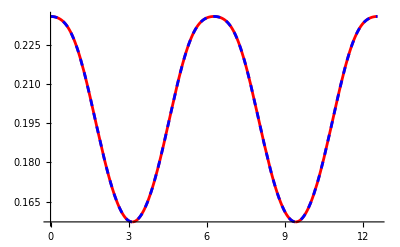

```mathematica
Show[Plot[corrPC["δrpar"][wr],{wr,0,4π},PlotStyle->Red],Plot[corrPCGeneric["δrpar"][wr,23],{wr,0,4π},PlotStyle->{Blue,Dashed}]]
```

```mathematica
Show[Plot[corrPCFourier["δrpar"][wr],{wr,0,4π},PlotStyle->Red],Plot[corrPCGeneric["δrpar"][wr,23],{wr,0,4π},PlotStyle->{Blue,Dashed}]]
```

-Graphics-

#### Spin corrections to the radial velocities

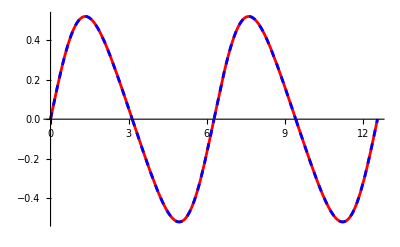

```mathematica
Show[Plot[corrPC["δvrpar"][wr],{wr,0,4π},PlotStyle->Red],Plot[corrPCGeneric["δvrpar"][wr,23],{wr,0,4π},PlotStyle->{Blue,Dashed}]]
```

```mathematica
Show[Plot[corrPCFourier["δvrpar"][wr],{wr,0,4π},PlotStyle->Red],Plot[corrPCGeneric["δvrpar"][wr,23],{wr,0,4π},PlotStyle->{Blue,Dashed}]]
```

-Graphics-

#### Spin corrections to the coordinate time and azimuthal trajectories - purely oscillatory term

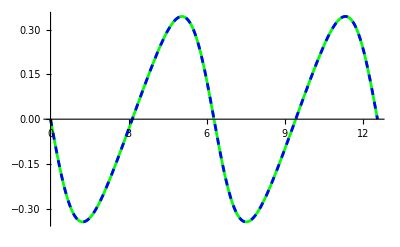

```mathematica
Show[Plot[corrPC["Δδtpar"][wr],{wr,0,4π},PlotStyle->Green],Plot[corrPCGeneric["Δδtpar"][wr,23],{wr,0,4π},PlotStyle->{Blue,Dashed}]]
```

```mathematica
corrPCGeneric["Δδtpar"][wr,0]//Simplify//N
```

-0.332439 Sin[wr]-0.114601 Cos[wr] Sin[wr]-0.00874424 Sin[3. wr]-0.00123444 Sin[4. wr]-0.0001651 Sin[5. wr]-0.0000212814 Sin[6. wr]-2.67156×10^-6 Sin[7. wr]-3.28804×10^-7 Sin[8. wr]-3.98531×10^-8 Sin[9. wr]-4.77197×10^-9 Sin[10. wr]-5.65757×10^-10 Sin[11. wr]-6.65264×10^-11 Sin[12. wr]

```mathematica
corrPCFourier["Δδtpar"][wr]//Simplify//N
```

-0.332439 Sin[wr]-0.114601 Cos[wr] Sin[wr]-0.00874424 Sin[3. wr]-0.00123444 Sin[4. wr]-0.0001651 Sin[5. wr]-0.0000212814 Sin[6. wr]-2.67156×10^-6 Sin[7. wr]-3.28804×10^-7 Sin[8. wr]-3.98531×10^-8 Sin[9. wr]-4.77197×10^-9 Sin[10. wr]-5.65757×10^-10 Sin[11. wr]-6.65264×10^-11 Sin[12. wr]

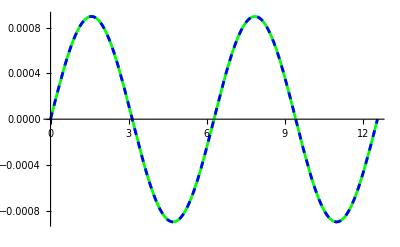

```mathematica
Show[Plot[corrPC["Δδϕpar"][wr],{wr,0,4π},PlotStyle->Green],Plot[corrPCGeneric["Δδϕpar"][wr,23],{wr,0,4π},PlotStyle->{Blue,Dashed}]]
```

```mathematica
corrPCGeneric["Δδϕpar"][wr,0]//Simplify//N
```

0.000898931 Sin[wr]-8.99935×10^-7 Cos[wr] Sin[wr]+5.34975×10^-7 Sin[3. wr]-2.17901×10^-10 Sin[4. wr]-2.82504×10^-13 Sin[5. wr]-1.02248×10^-14 Sin[6. wr]+3.94797×10^-17 Sin[7. wr]

```mathematica
corrPCFourier["Δδϕpar"][wr]//Simplify//N
```

0.000898931 Sin[wr]-8.99935×10^-7 Cos[wr] Sin[wr]+5.34975×10^-7 Sin[3. wr]-2.17901×10^-10 Sin[4. wr]-2.82504×10^-13 Sin[5. wr]-1.02248×10^-14 Sin[6. wr]+3.94804×10^-17 Sin[7. wr]

#### Spin corrections to the coordinate time and azimuthal velocities

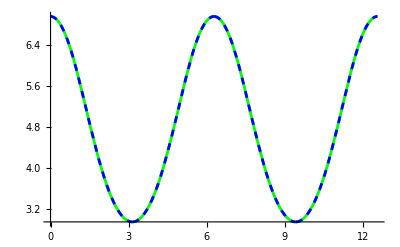

```mathematica
Show[Plot[corrPC["δvtpar"][wr],{wr,0,4π},PlotStyle->Green],Plot[corrPCGeneric["δvtpar"][wr,23],{wr,0,4π},PlotStyle->{Blue,Dashed}]]
```

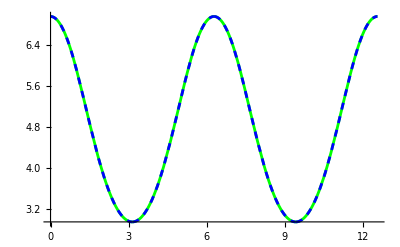

```mathematica
Show[Plot[corrPCFourier["δvtpar"][wr],{wr,0,4π},PlotStyle->Green],Plot[corrPCGeneric["δvtpar"][wr,23],{wr,0,4π},PlotStyle->{Blue,Dashed}]]
```

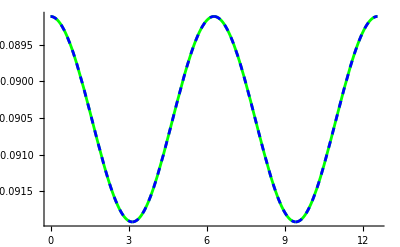

```mathematica
Show[Plot[corrPC["δvϕpar"][wr],{wr,0,4π},PlotStyle->Green],Plot[corrPCGeneric["δvϕpar"][wr,23],{wr,0,4π},PlotStyle->{Blue,Dashed}]]
```

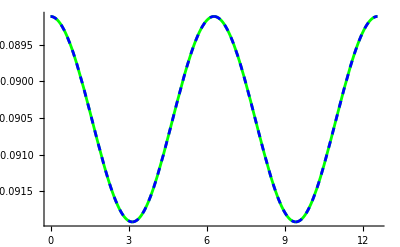

```mathematica
Show[Plot[corrPCFourier["δvϕpar"][wr],{wr,0,4π},PlotStyle->Green],Plot[corrPCGeneric["δvϕpar"][wr,23],{wr,0,4π},PlotStyle->{Blue,Dashed}]]
```

### Spin corrections orthogonal component of the spin

Mino-time precession frequency

```mathematica
corrPC["MinoPrecessionFrequency"]
```

3.467352990830548192488680888772287250288

Precession phase

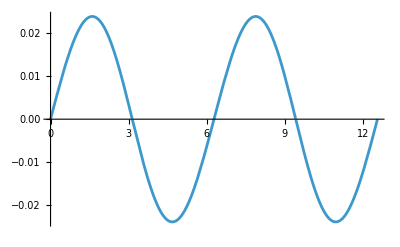

```mathematica
Plot[corrPC["ψp"][wr],{wr,0,4π}]
```

Spin correction to the polar motion

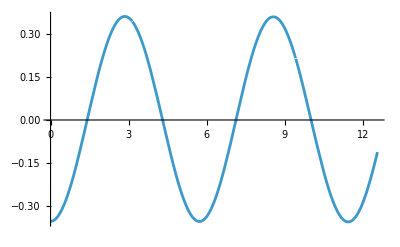

```mathematica
Plot[corrPC["δzort"][wr],{wr,0,4π}]
```

## Homoclinic orbits

IMPORTANT NOTE: all the functions for the orbits take as input the mean anomalies w_r and w_z. The input of the following functions are:

- primary spin “a”
- semi-latus rectum “p”
- eccentricity “e”
- inclination “x” defined as  x=Sign[L_z]√(1-z_1^2)

Location of the geodesic separatrix

```mathematica
psepgeo=KerrGeoSeparatrix[0.9`45,0.2`45,1]
```

2.500762004518768859047291151271885636861036

```mathematica
r1geo=psepgeo/(1-e)/.e->0.2`45;
r2geo=psepgeo/(1+e)/.e->0.2`45;
```

### Calculation orbits

```mathematica
AbsoluteTiming[corrPCHom=KerrNearEqSpinOrbitCorrPCHom[0.9`45,psepgeo,0.2`45,1];]
```

{0.009673,Null}

```mathematica
AbsoluteTiming[corrPCNearHom=KerrNearEqSpinOrbitCorrPCPer[0.9`45,psepgeo+10^(-10),0.2`45,1];]
```

{0.016827,Null}

### Constants of motion and frequencies

```mathematica
{corrPCHom["Eg"],corrPCHom["Lzg"]}
```

{0.851937710763679755967062536438040419823937,2.131021461208354245983283254061270631199}

Mino-time frequencies. Order of appearance: Υ_t , Υ_r , Υ_z , Υ_ϕ

```mathematica
corrPCHom["MinoFrequenciesGeo"]
```

{14.16029083867631630281444643098820834919,0,2.182511443058974949971131852788677663617,3.623033306497456377864552649150270055197}

BL frequencies. Order of appearance:  Ω_r , Ω_z , Ω_ϕ

```mathematica
corrPCHom["BLFrequenciesGeo"]
```

{0,0.1541289983322823468452935653006304784264,0.2558586788769751243243135520881135155592}

### Shifts constants of motion

```mathematica
{corrPCHom["Es"],corrPCHom["Jzs"]}
```

{-0.096390791292798374720815618225506616561,0.0217149505510818858014353988722125678}

```mathematica
{corrPCNearHom["Es"],corrPCNearHom["Jzs"]}
```

{-0.0963907912896649211908948636077049734434,0.0217149505607665788607765133951782139}

### Shifts frequencies

Mino-time frequencies. Order of appearance: Υ_t  , Υ_ϕ

```mathematica
corrPCHom["MinoFrequenciesCorrection"]
```

{-3.30950165622577904106654288054942795,0.4747086691138251538134901376269318335}

BL frequencies. Order of appearance:   Ω_ϕ

```mathematica
corrPCHom["BLFrequenciesCorrection"]
```

{0.09332247519998279316445367937918086258}

```mathematica
corrPCNearHom["MinoFrequenciesCorrection"]
```

{-3.87681446699434313564,0.0239328499848731126819,0.375692835340504301141}

```mathematica
corrPCNearHom["BLFrequenciesCorrection"]
```

{0.00349738875718827616712,0.0924658312594147504616}

### Geodesic coordinate time and azimuthal trajectories

```mathematica
{corrPCHom[ "trg"][r1geo],corrPCHom[ "ϕrg"][r1geo]}
```

{0.,0.}

The coordinate time and azimuthal trajectories diverge logarithmically at the periastron

```mathematica
{corrPCHom[ "trg"][r2geo],corrPCHom[ "ϕrg"][r2geo]}
```

{Indeterminate,Indeterminate}

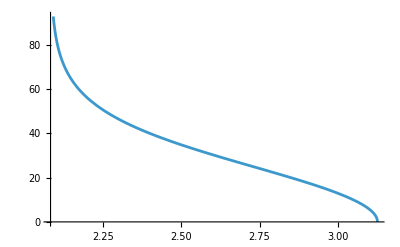

```mathematica
Plot[corrPCHom[ "trg"][r],{r,r2geo,r1geo}]
```

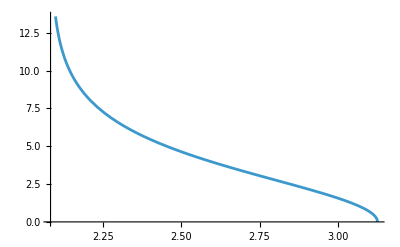

```mathematica
Plot[corrPCHom[ "ϕrg"][r],{r,r2geo,r1geo}]
```

### Spin corrections parallel component of the spin

#### Spin corrections to the radial trajectories

Note: the correction to the radial motion, δr(r_g), is  defined at r_g=r_(2g) only if they are parametrized using the Mino-time λ.  δr(r_g) is not defined at when parametrized using the geodesic radial coordinate r_g. However,  δr(r_g) is finite in the limit r_g->r_(2g)

The correction to the radial motion is finite near the periastron

```mathematica
{corrPCHom["δrpar"][r2geo+10^-24],corrPCHom["δrpar"][r1geo]}
```

{-0.91918470119607743687930658430394005551,-1.3787770517941161553189395534908249466}

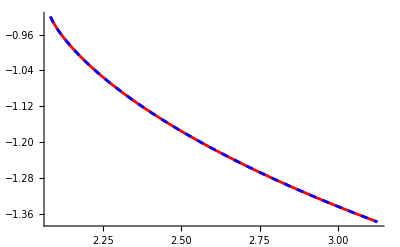

```mathematica
Show[Plot[corrPCHom["δrpar"][r],{r,r2geo,r1geo},PlotStyle->Red],Plot[corrPCNearHom["δrOfrpar"][r],{r,r2geo,r1geo},PlotStyle->{Blue,Dashed}]]
```

#### Spin corrections to the radial velocity

Note: the shift to the radial velocity, dδr/dλ, is defined at r_g=r_(2g) only if it is parametrized using the Mino-time λ. dδr/dλ is not defined at  r_g=r_(2g) when parametrized using the geodesic radial coordinate r_g. However, dδr/dλ is finite in the limit r_g->r_(2g)

```mathematica
{corrPCHom["δvrpar"][r2geo+10^-16],corrPCHom["δvrpar"][r1geo-10^-16]}
```

{-6.882954043×10^-16,-2.54424325×10^-9}

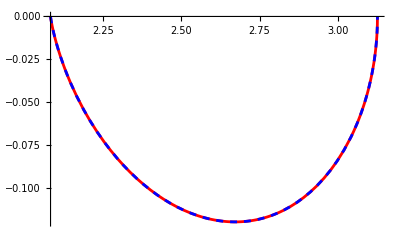

```mathematica
Show[Plot[corrPCHom["δvrpar"][r],{r,r2geo,r1geo},PlotStyle->Red],Plot[corrPCNearHom["δvrOfrpar"][r],{r,r2geo,r1geo},PlotStyle->{Blue,Dashed}]]
```

#### Spin corrections to the coordinate time and azimuthal trajectories

The shifts to the coordinate time and azimuthal trajectories diverge logarithmically at the periastron, as the corresponding geodesic trajectories

```mathematica
{corrPCHom["δtpar"][r2geo],corrPCHom["δtpar"][r1geo-10^(-14)]}
```

Power::infy: Infinite expression 1/0. encountered.

{Indeterminate,-2.2794036287683×10^-6}

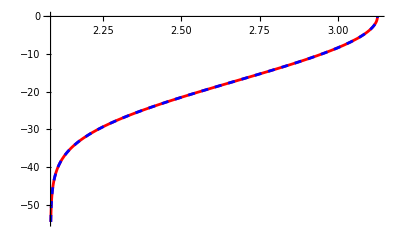

```mathematica
Show[Plot[corrPCHom["δtpar"][r],{r,r2geo,r1geo},PlotStyle->Red],Plot[corrPCNearHom["δtOfrpar"][r],{r,r2geo,r1geo},PlotStyle->{Blue,Dashed}]]
```

```mathematica
{corrPCHom["δϕpar"][r2geo],corrPCHom["δϕpar"][r1geo-10^(-14)]}
```

Power::infy: Infinite expression 1/0. encountered.

{Indeterminate,-8.706199398991×10^-8}

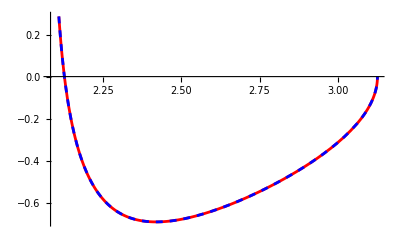

```mathematica
Show[Plot[corrPCHom["δϕpar"][r],{r,r2geo,r1geo},PlotStyle->Red],Plot[corrPCNearHom["δϕOfrpar"][r],{r,r2geo,r1geo},PlotStyle->{Blue,Dashed}]]
```

#### Spin corrections to the coordinate time and azimuthal velocities

Note: the shift to the coordinate time, dδt/dλ, and azimuthal velocities,dδϕ/dλ, are defined at r_g=r_(2g) only if they are parametrized using the Mino-time λ. dδt/dλ and dδϕ/dλ are not defined at when parametrized using the geodesic radial coordinate r_g. However, dδt/dλ and dδϕ/dλ are finite in the limit r_g->r_(2g)

The shift to the coordinate time velocity is finite near the periastron

```mathematica
{corrPCHom["δvtpar"][r2geo+10^-24],corrPCHom["δvtpar"][r1geo]}
```

{-3.3095016562257790410665621262949982656,-10.994588144041983859594620997197682574}

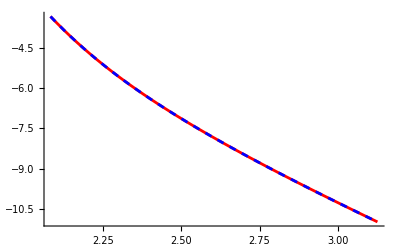

```mathematica
Show[Plot[corrPCHom["δvtpar"][r],{r,r2geo,r1geo},PlotStyle->Red],Plot[corrPCNearHom["δvtOfrpar"][r],{r,r2geo,r1geo},PlotStyle->{Blue,Dashed}]]
```

The shift to the azimuthal velocity is finite near the periastron

```mathematica
{corrPCHom["δvϕpar"][r2geo+10^-24],corrPCHom["δvϕpar"][r1geo]}
```

{0.47470866911382515381351006596815214899,-0.41993912567181713432578443996043315819}

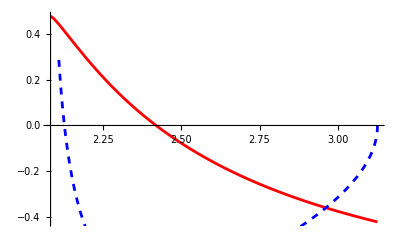

```mathematica
Show[Plot[corrPCHom["δvϕpar"][r],{r,r2geo,r1geo},PlotStyle->Red],Plot[corrPCNearHom["δvϕOfrpar"][r],{r,r2geo,r1geo},PlotStyle->{Blue,Dashed}]]
```

### Spin corrections orthogonal component of the spin

Mino-time precession frequency

```mathematica
corrPCHom["MinoPrecessionFrequency"]
```

1.443595627971688631771498557704924076042

Precession phase. It diverges logarithmically at the periastron

```mathematica
{corrPCHom["ψp"][r2geo],corrPCHom["ψp"][r1geo]}
```

{Indeterminate,0.}

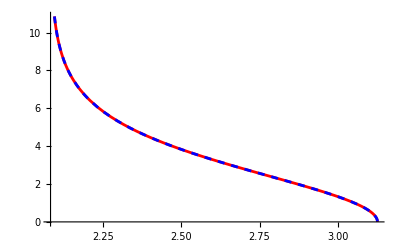

```mathematica
Show[Plot[corrPCHom["ψp"][r],{r,r2geo,r1geo},PlotStyle->Red],Plot[corrPCNearHom["ψpOfr"][r],{r,r2geo,r1geo},PlotStyle->{Blue,Dashed}]]
```

Spin correction to the polar motion

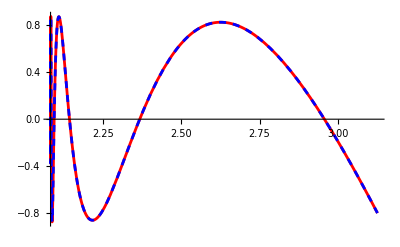

```mathematica
Show[Plot[corrPCHom["δzort"][r],{r,r2geo,r1geo},PlotStyle->Red],Plot[corrPCNearHom["δzOfrort"][r],{r,r2geo,r1geo},PlotStyle->{Blue,Dashed}]]
```

## Plots orbits